```mathematica
Clear["Global`*"];
```

```mathematica
cplA=.3;(*heat capacity of liquid, component A, kJ/mol*K*)
cplB=.3;(*heat capacity of liquid, component B, kJ/mol*K*)
cpvA=.3;(*heat capacity of vapor, component A, kJ/mol*K*)
cpvB=.3;(*heat capacity of vapor,component B, kJ/mol*K*)

γA=12;(*heat of vaporization, component A, kJ/mol*)
γB=12; (*heat of vaporization, component B, J/mol*)
f1=77.3;
f2[x_]:=-179.43x^2+112.39x+59.96;(*bottom left - alpha liquid phase bottom line*)
f3[x_]:=-506.61x^2+815.78x-251.09;(*bottom right - beta liquid phase bottom line*)
f4[x_]:=-382.08*x^3+253.87*x^2-113.1*x+97.252;(*top left - alpha phase bubble point*)
f5[x_]:=-32.008*x^2-13.96*x+97.312;(*alpha phase dew point*)
f6[x_]:=-30*x^2+86.675*x+36.095;(*beta phase dew point*)
f7[x_]:=294.89*x^2-451.53*x+249.41;

(*top right - beta phase bubble point*)
```

```mathematica
heatαsensible1[ζ_]:=(cpvB/(cpvB+cplB)(ζ*cpvB+(1-ζ)*cpvA)+cplB/(cpvB+cplB)(ζ*cplB+(1-ζ)*cplA))*(f5[ζ]-f4[ζ]);
heatαsensible2[ζ_]:=(cpvB/(cpvB+cplB)(ζ*cpvB+(1-ζ)*cpvA)+cplB/(cpvB+cplB)(ζ*cplB+(1-ζ)*cplA))*(f5[ζ]-77.3);
heatβsensible1[ζ_]:=(cpvB/(cpvB+cplB)(ζ*cpvB+(1-ζ)*cpvA)+cplB/(cpvB+cplB)(ζ*cplB+(1-ζ)*cplA))*(f6[ζ]-77.3);
heatβsensible2[ζ_]:=(cpvB/(cpvB+cplB)(ζ*cpvB+(1-ζ)*cpvA)+cplB/(cpvB+cplB)(ζ*cplB+(1-ζ)*cplA))*(f6[ζ]-f7[ζ]);


(*Amount of heat required to reach the "horizontal line"*)
heat1liquid[ζ_]:=(77.3-70)*(ζ*cplB+(1-ζ)*cplA);


(*Amount of heat required to reach said line and fully vaporize one of two liquid phases*)
heat1alpha[ζ_]:=heat1liquid[ζ]+(ζ-0.2752)/(.6-0.2752)*(.6*γB+.4*γA);
heat1beta[ζ_]:=heat1liquid[ζ]+(.8109-ζ)/(.8109-.6)*(.6*γB+.4*γA);

(*Amount of heat required to get to any given line*)
```

```mathematica
heat2[ζ_]:=(f2[ζ]-70)*(ζ*cplB+(1-ζ)*cplA);
heat3[ζ_]:=(f3[ζ]-70)*(ζ*cplB+(1-ζ)*cplA);
heat4[ζ_]:=(f4[ζ]-70)*(ζ*cplB+(1-ζ)*cplA);
heat5a[ζ_]:=heat4[ζ]+ζ*γB+(1-ζ)*γA+heatαsensible1[ζ];
heat5b[ζ_]:=heat1liquid[ζ]+heatαsensible2[ζ]+ζ*γB+(1-ζ)*γA;
heat7[ζ_]:=(f7[ζ]-70)*(ζ*cplB+(1-ζ)*cplA);
heat6a[ζ_]:=heat1liquid[ζ]+heatβsensible1[ζ]+ζ*γB+(1-ζ)*γA;
heat6b[ζ_]:=heat7[ζ]+ζ*γB+(1-ζ)*γA+heatβsensible2[ζ];
```

```mathematica
(*Calculates temperature in the 2-phase VLE regions. Done with interpolation - not perfect, but it works for demonstration purposes*)
alphaVLEa[z_,heat_,T0_]:=((heat-heat4[z])/(heat5a[z]-heat4[z]))*(f5[z]-T0)+T0;
alphaVLEb[z_,heat_,T0_]:=((heat-heat1alpha[z])/(heat5b[z]-heat1alpha[z]))*(f5[z]-T0)+T0;

betaVLEa[z_,heat_,T0_]:=((heat-heat1beta[z])/(heat6a[z]-heat1beta[z]))*(f6[z]-T0)+T0;
betaVLEb[z_,heat_,T0_]:=((heat-heat7[z])/(heat6b[z]-heat7[z]))*(f6[z]-T0)+T0;
```

```mathematica
(*I am using a second order polynomial to model how much heat is required to reach each line. In other words, it is a less computationally heavy method of calculating the values above*)
```

```mathematica
model=a+b*ζ+c*ζ^2;
```

```mathematica
(*The constants that fit into the model for each line*)
```

```mathematica
heat2ApproxConstants=FindFit[Table[{z,heat2[z]},{z,0.1,.276,.001}],model,{a,b,c},ζ];
heat3ApproxConstants=FindFit[Table[{z,heat3[z]},{z,.811,.92,.001}],model,{a,b,c},ζ];
heat4ApproxConstants=FindFit[Table[{z,heat4[z]},{z,0,.276,.001}],model,{a,b,c},ζ];
heat5ApproxConstants=FindFit[Table[{z,heat5a[z]},{z,0,.276,.001}],model,{a,b,c},ζ];
heat6ApproxConstants=FindFit[Table[{z,heat6a[z]},{z,.6,.811,.001}],model,{a,b,c},ζ];
heat7ApproxConstants=FindFit[Table[{z,heat7[z]},{z,.811,1,.001}],model,{a,b,c},ζ];
```

```mathematica
(*These are the polynomial models fully written out*)
```

```mathematica
heat2Poly[ζ_]=Evaluate[model/.heat2ApproxConstants];
```

```mathematica
Input2=SetPrecision[InputForm[heat2Poly[ζ],NumberMarks->False],4]
```

-3.012 + 33.717*ζ - 53.829*ζ^2

```mathematica
heat3Poly[ζ_]=Evaluate[model/.heat3ApproxConstants];
```

```mathematica
Input3=SetPrecision[InputForm[heat3Poly[ζ],NumberMarks->False],4]
```

-96.327 + 244.73*ζ - 151.98*ζ^2

```mathematica
heat4Poly[ζ_]=Evaluate[model/.heat4ApproxConstants];
```

```mathematica
Input4=SetPrecision[InputForm[heat4Poly[ζ],NumberMarks->False],4]
```

8.0564 - 28.701*ζ + 28.707*ζ^2

```mathematica
heat5Poly[ζ_]=Evaluate[model/.heat5ApproxConstants];
```

```mathematica
Input5=SetPrecision[InputForm[heat5Poly[ζ],NumberMarks->False],4]
```

20.194 - 4.188*ζ - 9.6024*ζ^2

```mathematica
heat6Poly[ζ_]=Evaluate[model/.heat6ApproxConstants];
```

```mathematica
Input6=SetPrecision[InputForm[heat6Poly[ζ],NumberMarks->False],4]
```

1.8285 + 26.003*ζ - 9.*ζ^2

```mathematica
heat7Poly[ζ_]=Evaluate[model/.heat7ApproxConstants];
```

```mathematica
Input7=SetPrecision[InputForm[heat7Poly[ζ],NumberMarks->False],4]
```

53.823 - 135.46*ζ + 88.467*ζ^2

```mathematica
(*ClearAll["Global`*"];*)
```

```mathematica
model2=a+b*ζ+c*ζ^2+d*H+e*H^2+f*H*ζ;
```

```mathematica
(*x-value solution for line #4, .02 < x <.276*)
```

```mathematica
H=heat4[.02];
ζ=.02;
i=1;

While[ζ<.276,
While[H<heat5a[ζ],
heat4Atable[i]={ζ,H,x/.FindRoot[f4[x]==alphaVLEa[ζ,H,f4[ζ]],{x,.001,.276}]};
i++;H=H+.05];
ζ=ζ+.005;
H=heat4[ζ]];
heat4Amatch=Table[heat4Atable[j],{j,1,i-1}];
Clear[ζ];
Clear[H];
heat4AsolVars=FindFit[heat4Amatch,model2,{a,b,c,d,e,f},{ζ,H}];
heat4AsolNew=model2/.heat4AsolVars;
Input4bA=SetPrecision[InputForm[heat4AsolNew,NumberMarks->False],4]
```

0.045249 - 0.0051401*H + 0.00014097*H^2 + 1.0397*ζ - 0.041867*H*ζ - 0.22776*ζ^2

```mathematica
(*x-value solution for line #4, .276< x <.6*)
```

```mathematica
H=heat1alpha[.276];
ζ=.276;
i=1;

While[ζ<.6,
While[H<heat5b[ζ],
heat4Btable[i]={ζ,H,x/.FindRoot[f4[x]==alphaVLEb[ζ,H,77.3],{x,.001,.276}]};
i++;H=H+.05];
ζ=ζ+.005;
H=heat1alpha[ζ]];
heat4Bmatch=Table[heat4Btable[j],{j,1,i-1}];
Clear[ζ];
Clear[H];
heat4BsolVars=FindFit[heat4Bmatch,model2,{a,b,c,d,e,f},{ζ,H}];
heat4BsolNew=model2/.heat4BsolVars;
Input4bB=SetPrecision[InputForm[heat4BsolNew,NumberMarks->False],4]
```

0.17659 - 0.011403*H + 0.00015764*H^2 + 0.36573*ζ - 0.019506*H*ζ + 0.49385*ζ^2

```mathematica
(*x-value solution for line #5, .02 < x <.276*)
```

```mathematica
H=heat4[.02];
ζ=.02;
i=1;

While[ζ<.276,
While[H<heat5a[ζ],
heat5Atable[i]={ζ,H,x/.FindRoot[f5[x]==alphaVLEa[ζ,H,f4[ζ]],{x,.02,.6}]};
i++;H=H+.05];
ζ=ζ+.005;
H=heat4[ζ]];
heat5Amatch=Table[heat5Atable[j],{j,1,i-1}];
Clear[ζ];
Clear[H];
heat5AsolVars=FindFit[heat5Amatch,model2,{a,b,c,d,e,f},{ζ,H}];
heat5AsolNew=model2/.heat5AsolVars;
Input5bA=SetPrecision[InputForm[heat5AsolNew,NumberMarks->False],4]
```

0.18341 - 0.0047808*H - 0.00032185*H^2 + 2.4859*ζ - 0.037626*H*ζ - 3.0051*ζ^2

```mathematica
(*x-value solution for line #5, .276 < x <.6*)
```

```mathematica
H=heat1alpha[.277];
ζ=.276;
i=1;

While[ζ<.6,
While[H<heat5b[ζ],
heat5Btable[i]={ζ,H,x/.FindRoot[f5[x]==alphaVLEb[ζ,H,77.3],{x,.276,.6}]};
i++;H=H+.05];
ζ=ζ+.005;
H=heat1alpha[ζ]];
heat5Bmatch=Table[heat5Btable[j],{j,1,i-1}];
Clear[ζ];
Clear[H];
heat5BsolVars=FindFit[heat5Bmatch,model2,{a,b,c,d,e,f},{ζ,H}];
heat5BsolNew=model2/.heat5BsolVars;
Input5bB=SetPrecision[InputForm[heat5BsolNew,NumberMarks->False],4]
```

0.48375 - 0.016624*H - 0.00029187*H^2 + 0.53265*ζ + 0.0094265*H*ζ + 0.035314*ζ^2

```mathematica
(*x-value solution for line #6, .6 < x <.811*)
```

```mathematica
H=heat1beta[.61];
ζ=.61;
i=1;

While[ζ<.811,
While[H<heat6a[ζ],
heat6Atable[i]={ζ,H,x/.FindRoot[f6[x]==betaVLEa[ζ,H,77.3],{x,.6,1}]};
i++;H=H+.05];
ζ=ζ+.005;
H=heat1beta[ζ]];
heat6Amatch=Table[heat6Atable[j],{j,1,i-1}];
Clear[ζ];
Clear[H];
heat6AsolVars=FindFit[heat6Amatch,model2,{a,b,c,d,e,f},{ζ,H}];
heat6AsolNew=model2/.heat6AsolVars;
Input6bA=SetPrecision[InputForm[heat6AsolNew,NumberMarks->False],4]
```

0.01099 + 0.0057346*H + 0.0001327*H^2 + 0.70827*ζ + 0.0072841*H*ζ - 0.017014*ζ^2

```mathematica
(*x-value solution for line #6, .811 < x < 1 *)
```

```mathematica
H=heat7[.812];
ζ=.811;
i=1;

While[ζ<.98,
While[H<heat6b [ζ],
heat6Btable[i]={ζ,H,x/.FindRoot[f6[x]==betaVLEb[ζ,H,f7[ζ]],{x,.6,1}]};
i++;H=H+.05];
ζ=ζ+.005;
H=heat7[ζ]];
heat6Bmatch=Table[heat6Btable[j],{j,1,i-1}];
Clear[ζ];
Clear[H];
heat6BsolVars=FindFit[heat6Bmatch,model2,{a,b,c,d,e,f},{ζ,H}];
heat6BsolNew=model2/.heat6BsolVars;
Input6bB=SetPrecision[InputForm[heat6BsolNew,NumberMarks->False],4]
```

3.1409 + 0.048378*H + 0.00012452*H^2 - 7.2073*ζ - 0.04249*H*ζ + 4.9543*ζ^2

```mathematica
(*x-value solution for line #7, .6 < x < .811 *)
```

```mathematica
H=heat1beta[.61];
ζ=.61;
i=1;

While[ζ<.811,
While[H<heat6a[ζ],
heat7Atable[i]={ζ,H,x/.FindRoot[f7[x]==betaVLEa[ζ,H,77.3],{x,.81,1}]};
i++;H=H+.05];
ζ=ζ+.005;
H=heat1beta[ζ]];
heat7Amatch=Table[heat7Atable[j],{j,1,i-1}];
Clear[ζ];
Clear[H];
heat7AsolVars=FindFit[heat7Amatch,model2,{a,b,c,d,e,f},{ζ,H}];
heat7AsolNew=model2/.heat7AsolVars;
Input7bA=SetPrecision[InputForm[heat7AsolNew,NumberMarks->False],4]
```

-0.87649 + 0.053699*H - 0.00038079*H^2 + 3.2127*ζ - 0.046979*H*ζ - 1.431*ζ^2

```mathematica
(*x-value solution for line #7, .811 < x < 1 *)
```

```mathematica
H=heat7[.811];
ζ=.811;
i=1;

While[ζ<.98,
While[H<heat6b[ζ],
heat7Btable[i]={ζ,H,x/.FindRoot[f7[x]==betaVLEb[ζ,H,f7[ζ]],{x,.81,1}]};
i++;H=H+.1];
ζ=ζ+.01;
H=heat7Poly[ζ]];
heat7Bmatch=Table[heat7Btable[j],{j,1,i-1}];
Clear[ζ];
Clear[H];
heat7BsolVars=FindFit[heat7Bmatch,model2,{a,b,c,d,e,f},{ζ,H}];
heat7BsolNew=model2/.heat7BsolVars;
Input7bB=SetPrecision[InputForm[heat7BsolNew,NumberMarks->False],4]
```

0.68355 + 0.042927*H - 0.00014275*H^2 - 0.47087*ζ - 0.038497*H*ζ + 0.75525*ζ^2

```mathematica
(*This is the z-value on each line the corresponds to a given heat. It is essentially the inverse of the equations above. Used to calculate the lever rule*)
```

```mathematica
heat2sol[H_]=Quiet[zsol/.Solve[H-heat2Poly[zsol]==0,zsol][[1]]];
```

```mathematica
Input2b=SetPrecision[InputForm[heat2sol[ζ],NumberMarks->False],4]
```

0.000027866*(11239. - 1.*Sqrt[5.4256*^7 - 2.3924*^7*ζ])

```mathematica
heat3sol[H_]=Quiet[zsol/.Solve[H-heat3Poly[zsol]==0,zsol][[2]]];
```

```mathematica
Input3b=SetPrecision[InputForm[heat3sol[ζ],NumberMarks->False],4]
```

0.000019739*(40789. + 2.8284*Sqrt[4.6336*^6 - 2.1109*^6*ζ])

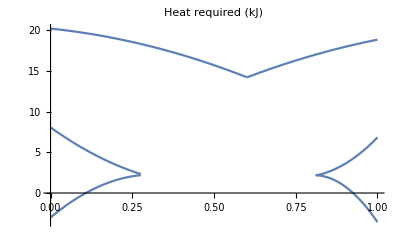

```mathematica
Show[{
Plot[heat2Poly[zed],{zed,0,.276}],
Plot[heat3Poly[zed],{zed,.811,1}],
Plot[heat4Poly[zed],{zed,0,.276}],
Plot[heat5Poly[zed],{zed,0,.6}],
Plot[heat6Poly[zed],{zed,.6,1}],
Plot[heat7Poly[zed],{zed,.811,1}]},PlotRange->All,PlotLabel->"Heat required (kJ)"]
```